# Project 7

## Question 2

Import the Data

```mathematica
A=ImageData[
Import["C:\\Users\\struther\\Desktop\\23-24-Classes\\Fall 2023 Courses\\SciComp\\peppers.png"]];
Image[A]
```

-Graphics-

## Code Bits

### CutOff: Input a vector of singular values and a scalar 0<p<1

Old fashioned loop.

```mathematica
σ=SingularValueList[A]; p=0.98;
energy=Accumulate[σ^2];energy=energy/energy⟦-1⟧;
k=1;
While[ energy⟦k⟧<p^2,k++]
{k,p^2,energy⟦1;;k⟧}
```

{7,0.9604,{0.859684,0.899142,0.923423,0.94054,0.952361,0.959361,0.964166}}

Computing an indicator.

```mathematica
σ=SingularValueList[A]; p=0.98;
energy=Accumulate[σ^2];energy=energy/energy⟦-1⟧;
k=FirstPosition[Sign[energy-p^2],1]⟦1⟧;
{k,p^2,energy⟦1;;k⟧}
```

{7,0.9604,{0.859684,0.899142,0.923423,0.94054,0.952361,0.959361,0.964166}}

There are lots of other ways to do the same thing.

```mathematica
CutOff[σ_,p_]:= Module[{energy=Accumulate[σ^2]},
energy=energy/energy⟦-1⟧;
FirstPosition[Sign[energy-p^2],1]⟦1⟧
]
```

Test the function.  This is a very minimal test!

```mathematica
σ=SingularValueList[A]; p=0.98;
CutOff[σ,p]
```

7

### SVDCompress: Input an array X, a block size b, and a scalar 0<p<1

I think the intention is that the inner blocks are square and of size b×b. The input array is probably not square. Our test problem is square! It is easy enough to count the sub pictures using modular arithmetic.   Here is a plot of the sub images demonstrating the required arithmetic.

```mathematica
{m,n}=Dimensions[A];
b=123;
{{q1,r1},{q2,r2}}=QuotientRemainder[{m,n},b];
MatrixPlot[A,ColorFunction->GrayLevel,Mesh->{b*Range[1,q1],b*Range[1,q2]}
]
```

-Graphics-

Here is a plot of the each of the sub images

```mathematica
GraphicsGrid[Table[
MatrixPlot[A⟦1+(i-1)*b;;i*b,1+(j-1)*b;;j*b⟧,ColorFunction->GrayLevel,Frame->False],
{i,1,q1},{j,1,q2}],
Spacings->{0,0}]
```

-Graphics-

So we know how to split up an image.  Lets see how to compress a single image.

```mathematica
{i,j}={2,3};
p=0.6;
AComp=A;
SubMat=AComp⟦1+(i-1)*b;;i*b,1+(j-1)*b;;j*b⟧;
{U,S,V}=SingularValueDecomposition[SubMat];
σ=Diagonal[S];
k=CutOff[σ,p]
B=U⟦All,1;;k⟧.S⟦1;;k,1;;k⟧.V⟦All,1;;k⟧ᵀ;
AComp⟦1+(i-1)*b;;i*b,1+(j-1)*b;;j*b⟧=B;
Image[AComp]
```

1

-Graphics-

```mathematica
Svd
```

```mathematica
σ=SingularValueList[A]; p=0.98;
energy=Accumulate[σ^2];energy=energy/energy⟦-1⟧;
k=1;
While[ energy⟦k⟧<p^2,k++]
{k,p^2,energy⟦1;;k⟧}
```

{7,0.9604,{0.859684,0.899142,0.923423,0.94054,0.952361,0.959361,0.964166}}

```mathematica
CutOff[sigma_,p_]:=Module[{
```

```mathematica
p={α,β,δ,γ}={1.1,0.4,0.1,0.4} ;
{x0,y0}={10.0,10.0};
{x02,y02}={11.0,11.0};
```

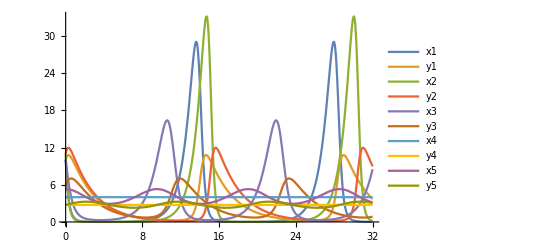

```mathematica
TMax=32;
{xSol1,ySol1}=NDSolveValue[{
x'[t]==α x[t]- β x[t] y[t],
y'[t]== δ x[t] y[t] -γ y[t],
x[0]==x0,
y[0]==y0 
},
{x,y}, {t, 0, TMax}];
{xSol2,ySol2}=NDSolveValue[{
x'[t]==α x[t]- β x[t] y[t],
y'[t]== δ x[t] y[t] -γ y[t],
x[0]==x02,
y[0]==y02
},
{x,y}, {t, 0, TMax}];
{xSol3,ySol3}=NDSolveValue[{
x'[t]==α x[t]- β x[t] y[t],
y'[t]== δ x[t] y[t] -γ y[t],
x[0]==10.0,
y[0]==6.0
},
{x,y}, {t, 0, TMax}];
{xSol4,ySol4}=NDSolveValue[{
x'[t]==α x[t]- β x[t] y[t],
y'[t]== δ x[t] y[t] -γ y[t],
x[0]==γ/δ,
y[0]==α/β
},
{x,y}, {t, 0, TMax}];
{xSol5,ySol5}=NDSolveValue[{
x'[t]==α x[t]- β x[t] y[t],
y'[t]== δ x[t] y[t] -γ y[t],
x[0]==γ/δ +1.3,
y[0]==α/β
},
{x,y}, {t, 0, TMax}];
Plot[{xSol1[t],ySol1[t],xSol2[t],ySol2[t],xSol3[t],ySol3[t],
xSol4[t],ySol4[t],xSol5[t],ySol5[t]},{t, 0, TMax},
PlotRange->All,
PlotLegends->{"x1","y1","x2","y2","x3","y3","x4","y4","x5","y5"}]
```

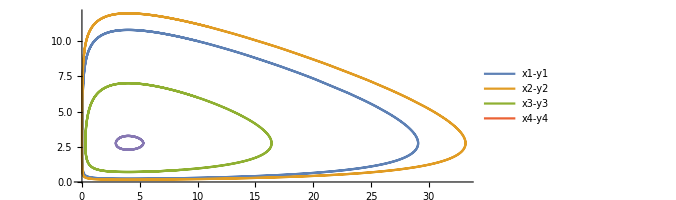

```mathematica
Pic=ParametricPlot[{{xSol1[t],ySol1[t]},
{xSol2[t],ySol2[t]},
{xSol3[t],ySol3[t]},
{xSol4[t],ySol4[t]},
{xSol5[t],ySol5[t]}
},
{t, 0, TMax},
PlotRange->All,
PlotLegends->{"x1-y1","x2-y2","x3-y3","x4-y4"}]
```